1. Naloga

```mathematica
v0 = {10, 3}
GG= 9.81
H = 10
a = {0, -GG}
x0 = {0, H}
```

{10,3}

9.81

10

{0,-9.81}

{0,10}

```mathematica
v[t_]:=v0+a *t 
(*v[t_]:={v0[[1]],v0[[2]]-GG*t*)
X[t_] :=x0 + v0 * t +(a*t^2)/2
```

```mathematica
v[1]
```

{10,-6.81}

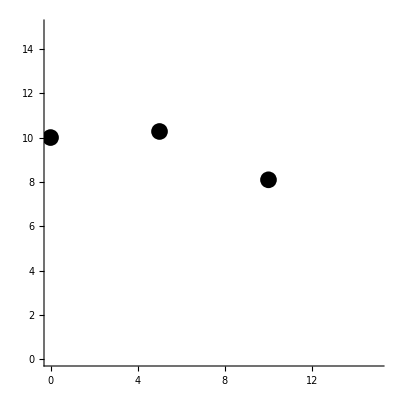

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]}
Graphics[{SlikaTocke[0],SlikaTocke[0.5],SlikaTocke[1]}, Axes->True, PlotRange->{{0,15},{0,15}}, AspectRatio->Automatic]
```

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,3}]
```

```mathematica
SlikaVektorja[t_] := Arrow[{X[t],X[t], v[t]}]
```

```mathematica
Manipulate[Graphics[SlikaVektorja[t],v[t]],Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,3}]
```

2. Naloga

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] := Hyperplane[n,v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
rx=Ravnina[{1,0,0},{0,0,0}]
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-